```mathematica
a:=RandomReal[{0,1}]
b:=RandomReal[{0,1}]
```

```mathematica
generate:={a,b};
```

```mathematica
check:=({x,y}=generate;If[0.0<(x^2-(2*x)+y)<0.1,check,{x,y}])
```

```mathematica
tab=Table[{0,0},{i,1,1000}];
```

```mathematica
For[i=1,i≤ 1000,i++,tab[[i]]=check]
```

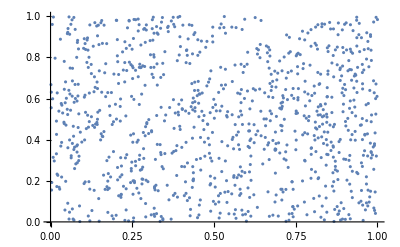

```mathematica
ListPlot[tab]
```